```mathematica
(*** Fighting Fantasy combat analysis -- dynamics without Luck-based control ***)
```

```mathematica
(*** theoretical victory probability ***)
```

```mathematica
prob =FullSimplify[pw^σopp Sum[Sum[pl^l pd^d Binomial[σopp-1+l,l] Binomial[σopp-1+l+d,d], {d, 0, ∞}], {l, 0, σhero-1}], Assumptions->{σopp∈Reals, σhero∈Reals, σopp>0, σhero>0}]
```

(1-pd)^-σopp pw^σopp ((1+pl/(-1+pd))^-σopp-(1-pd)^-σhero pl^σhero Binomial[-1+σhero+σopp,σhero] Hypergeometric2F1[1,σhero+σopp,1+σhero,-pl/(-1+pd)])

```mathematica
(*** read output of simulated dynamics ***)
```

```mathematica
l = ReadList["simscan.txt", {Number, Number, Number, Number}];
```

```mathematica
(*** use numerical expressions for dice roll probabilities and produce summary structure (vp with shero, sopp) ***)
```

```mathematica
outcomes = {1,4,10,20,35,56,80,104,125,140,146,140,125,104,80,56,35,20,10,4,1}/1296;
```

```mathematica
set = Table[{}, {i, 1, 20}];
For[Δ = -10,Δ ≤ 10, Δ++,
pl = pd = pw = 0;
For[i=1,i≤Length[outcomes],i++,
score = i-11;
If[score <Δ, pw += outcomes[[i]]];
If[score == Δ, pd += outcomes[[i]]];
If[score > Δ, pl += outcomes[[i]]];
];
set[[Δ+11]] = Table[Table[prob/.σhero->Ceiling[shero/2]/.σopp->Ceiling[sopp/2], {shero, 1, 24}], {sopp, 1, 24}];
];
```

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Set::partw: Part 21 of {{{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate},«22»,{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,«8»,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}},«18»,{«1»}} does not exist.

```mathematica
(*** produce summary structure from experimental outcomes ***)
```

```mathematica
eset = Table[Table[Table[0,{shero, 1, 30}], {sopp, 1, 30}], {i, 1, 21}];
count = 1;
For[Δ=-10, Δ≤10,Δ++,
For[shero=1,shero ≤ 30, shero++,
For[sopp=1,sopp≤30,sopp++,
eset[[Δ+11]][[sopp]][[shero]]=l[[count]][[4]];
count++;
];
];
];
```

```mathematica
(*** make some choices for graphical representation -- colour scheme and which kdiff to plot ***)
```

```mathematica
myHue[x_]:=Lighter[ColorData["ThermometerColors"][x]]
```

```mathematica
indices = {7,9, 11, 13, 15};
```

```mathematica
(*** produce figure ***)
```

```mathematica
g = Table[{Text["kdiff = "<>ToString[indices[[i]]-11]<>" eqn", {13, 30*i+27}], Text["kdiff = "<>ToString[indices[[i]]-11]<>" sim", {43, 30*i+27}],Table[Table[{myHue[set[[indices[[i]]]][[y]][[x]]],Rectangle[{x,30*i+y}, {x+1, 30*i+y+1}], myHue[eset[[indices[[i]]]][[y]][[x]]], Rectangle[{x+30,y+30*i}, {x+31, y+1+30*i}]}, {x, 1, 24}], {y, 1, 24}]}, {i, 1, Length[indices]}];
```

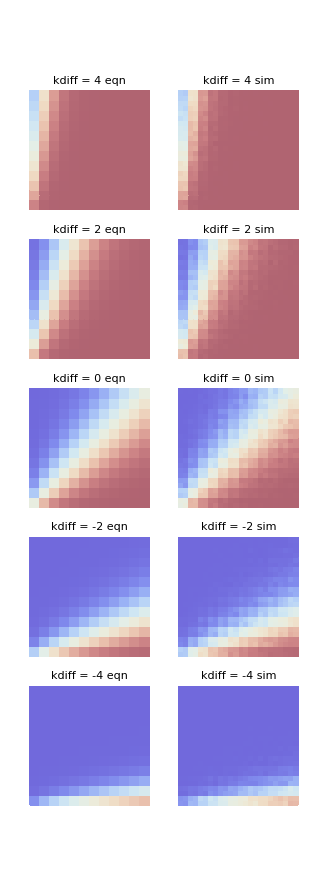

```mathematica
Graphics[g]
```

```mathematica
Export["simscan-compare.svg", Graphics[g], ImageSize->800]
```

simscan-compare.svg